4

{{0,1,2,0},{0,0,2,1}}

{{0,0},{1,0},{2,2},{0,1}}

{-x,-y,-2+2 x-y,-2-x+2 y}

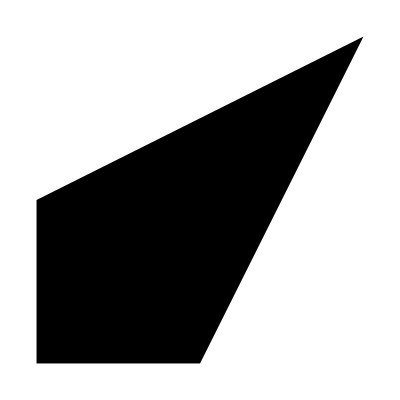

{1,K_2,K_3,K_4}

{1-K_2/2==0,(3 K_2)/2-K_3==0,K_3-(3 K_4)/2==0}

{{K_2→2,K_3→3,K_4→2}}

{(4-2 x-2 x^2-2 y+5 x y-2 y^2)/(4+2 x+2 y)}

x^2

{4 x-(3 (2 x+x^2))/(2+x+y)}

{(x (2+x+4 y))/(2+x+y)}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
m=Input[order]
xy={Table[Input[Subscript[x, i]],{i,m}],Table[Input[Subscript[y, i]],{i,m}]}
nodes=Transpose[xy]
Intercept[{x1_,y1_},{x2_,y2_}]:={y2-y1,x1-x2,-x1*y2+y1*x2}
nodesToIntercepts[p_?MatrixQ]:=Thread[Intercept[p,RotateRight[p]]]
nodesToLines[p_,{x_,y_}]:=-Dot[nodesToIntercepts[p],{x,y,1}]
ls=nodesToLines[nodes,{x,y}]
Graphics[Polygon[nodes]]
(*k1=1;k2=2;k3=8;k4=4;k5=3;*)
k=Table[Subscript[K, i],{i,m}]
ls[[0]]=ls[[m]];
For[i=1,i<m+1,i++,
If[i==1,num[i]= k[[i]]*Evaluate[∏_(j=3)^m ls[[j]]],
num[i]= k[[i]]*Evaluate[∏_(j=i+2)^(i+m-1) ls[[Mod[j,m]]]];
]]
deno=Sum[num[i],{i,m}];
g=#1&@@ xy;
h=#2&@@ xy;ClearAll[R,k1]
For[i=1,i<m,i++,e1=Mod[i+1,m];e2=Mod[i+2,m];
If[e2==0,R[m-2]=k[[m-1]]ls[[m-2]]-k[[m-2]]ls[[m]]/.{x->(g[[m-1]]+g[[m-2]])/2,y->(h[[m-1]]+h[[m-2]])/2},
If[e1==0,R[m-1]=k[[m]]ls[[m-1]]-k[[m-1]]ls[[1]]/.{x->(g[[m-1]]+g[[m]])/2,y->(h[[m-1]]+h[[m]])/2},
R[i]=k[[Mod[i+1,m]]]ls[[i]]-k[[i]]ls[[Mod[i+2,m]]]
/.{x->(g[[i]]+g[[Mod[i+1,m]]])/2,y->(h[[i]]+h[[Mod[i+1,m]]])/2};]]]
Subscript[K, 1]:=1
Table[R[i]==0,{i,m-1}]
Solve[%,Table[Subscript[K, i],{i,2,m}]]
For[i=1,i<m+1,i++,(Subscript[N,i]^1)[{x,y}]=Thread[Expand[num[i]]/Expand[deno]]/.%]
Print[(Subscript[N,1]^1)[{x,y}]]
f[{x_,y_}]=Input[function]
For[i=1,i<m+1,i++,a[i]=f[nodes[[i]]];
]
ClearAll[A1];
A1=Thread[Apart[Sum[a[i]*(Subscript[N,i]^1)[{x,y}],{i,1,m}]]]
Simplify[A1]
(*Plot3D[{A1,f[{x,y}]},{x,y}∈Polygon[nodes],ImageSize->500]*)
(*Function*)Plot3D[{f[{x,y}]},{x,y}∈Polygon[nodes],ImageSize->500]
(*Approximation*) Plot3D[{A1},{x,y}∈Polygon[nodes],ImageSize->500]
(*Error*)Plot3D[Abs[f[{x,y}]-A1],{x,y}∈Polygon[nodes],ImageSize->500]
```